# Origin of Attractive Interactions

```mathematica
ClearAll["Global`*"]
```

## Parameters

```mathematica
a=1;
t=1;
μ=-2.575;
```

## Definitions

```mathematica
ϵ[kx_,ky_]:=-2t(Cos[kx]+ Cos[ky])
```

```mathematica
f[kx_,ky_,β_]:=1/(Exp[β (ϵ[kx,ky]-μ)]+1)
```

```mathematica
L[kx_,ky_,qx_,qy_,β_]:=(f[kx,ky,β]-f[qx,qy,β])/(ϵ[kx,ky]-ϵ[qx,qy])
```

## Plots

```mathematica
Plot3D[L[kx,ky,0,0,1],{kx,-π,π},{ky,-π,π}]
```

-Graphics3D-

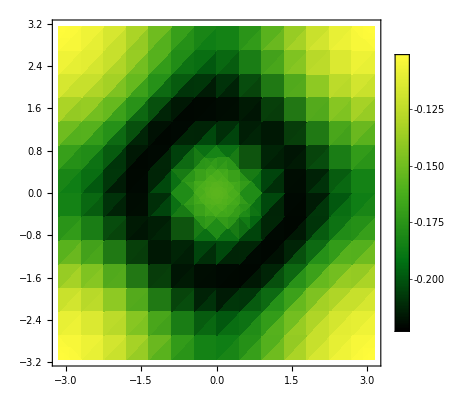

```mathematica
DensityPlot[L[kx,ky,0,0,1],{kx,-π,π},{ky,-π,π},ColorFunction->"AvocadoColors",PlotLegends->Automatic]
```

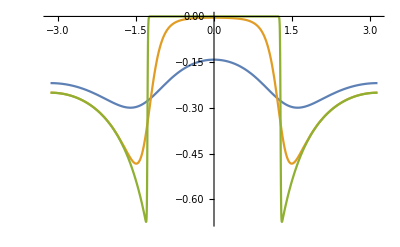

```mathematica
Plot[{L[kx,0,0,0,1.5],L[kx,0,0,0,5],L[kx,0,0,0,100]},{kx,-Pi,Pi}]
```

```mathematica
Rescale[0.2,{-0.3,0.3}]
```

0.833333